## 数据导入与初始化

### 数据导入

```mathematica
path = "/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp9";
SetDirectory[path]
```

```mathematica
For[i=0,i<=6,i++,
	If[i == 0,
		data = {Import["data/input/0.txt","Table"]},
		data = Join[data,{Import["data/input/"<>ToString[i]<>".txt","Table"]}]
	]
]
```

### 必要的函数

```mathematica
PlotRespectively[data_,legend_,place_,framelabel_,color_,range_] := ListLinePlot[data,Frame -> True, LabelStyle
     -> Directive[Black], GridLines -> Automatic, PlotLegends -> Placed[LineLegend[
    legend, LegendFunction -> Frame], place],FrameLabel->framelabel, PlotStyle -> ColorData[
    color, "ColorList"],PlotRange->range,PlotStyle->Thickness[0.01],FrameStyle->Thickness[0.003]];
    
PlotAll[data_,legends_,place_,framelabel_,color_,range_]:=Module[
	{list=data,l=Length[data],images,x,j},
	images=Array[x,Length[data]];
	For[j=1,j<=l,j++,
	images[[j]]=PlotRespectively[data[[j]],legends[[j]],place[[j]],framelabel[[j]],color,range[[j]]];
	];
	images
]

TableRefine[rawdata_]:=Module[
	{i,l=Length[rawdata],out,a,b,k},
	out = rawdata;
	For[i=1,i<=l,i++,
		out[[i,1]]=DateString[rawdata[[i,1]]]
    ];
    k = If[IntegerQ[l/2],l/2,l/2+1/2];
    a = Take[out,k];
    b = Take[out,k-l];
    Join[a,b,2]
]

LatexTable[datalist_]:=Module[
	{table,textable,i,l = If[IntegerQ[Length[datalist]/2],Length[datalist]/2,Length[datalist]/2+1/2]},
	table = TableRefine[datalist];
	For[i=1,i<=l,i++,
		If[i==1,
			textable = {StringReplace[ToString[table[[1]]],{","->"  & ","{"->"","}"->"  \\\\"}]},
			textable = Join[textable,{StringReplace[ToString[table[[i]]],{","->"  & ","{"->"","}"->"  \\\\"}]}]
		];
	];
	
	textable
]
```

```mathematica
Plot[Sin[x],{x,0,Pi},PlotStyle->Thickness[0.01],Frame->True,FrameStyle->Thickness[0.003]]
```

## 作图

```mathematica
legends = {"水-25 °C","正丁醇-0.4 ml","正丁醇-0.8 ml","正丁醇-1.2 ml","正丁醇-1.6 ml","正丁醇-2.0 ml","正丁醇-2.4 ml"};
place = Table[{0.85, 0.9},{i,7}];
framelabel = Table[{"时间 / t","压差 / pa"},{i,1,7}];
plotrange =Table[All,{i,1,7}];
```

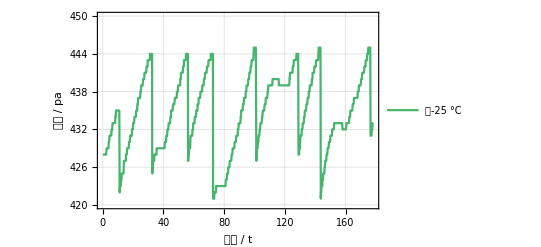

```mathematica
images = Array[a,7];
images[[1]] = PlotRespectively[data[[1]],{legends[[1]]},place[[1]],framelabel[[1]],97,{420,450}]
images[[2]] = PlotRespectively[data[[2]],{legends[[2]]},{0.8,0.9},framelabel[[2]],97,{374,388}];
images[[3]] = PlotRespectively[data[[3]],{legends[[3]]},{0.8,0.9},framelabel[[3]],97,{327,350}];
images[[4]] = PlotRespectively[data[[4]],{legends[[4]]},{0.8,0.9},framelabel[[4]],97,{{40,149},{314,324}}];
images[[5]] = PlotRespectively[data[[5]],{legends[[5]]},{0.8,0.9},framelabel[[5]],97,{275,297}];
images[[6]] = PlotRespectively[data[[6]],{legends[[6]]},{0.8,0.9},framelabel[[6]],97,{255,279}];
images[[7]] = PlotRespectively[data[[7]],{legends[[7]]},{0.8,0.9},framelabel[[7]],97,{243,261.5}];
```

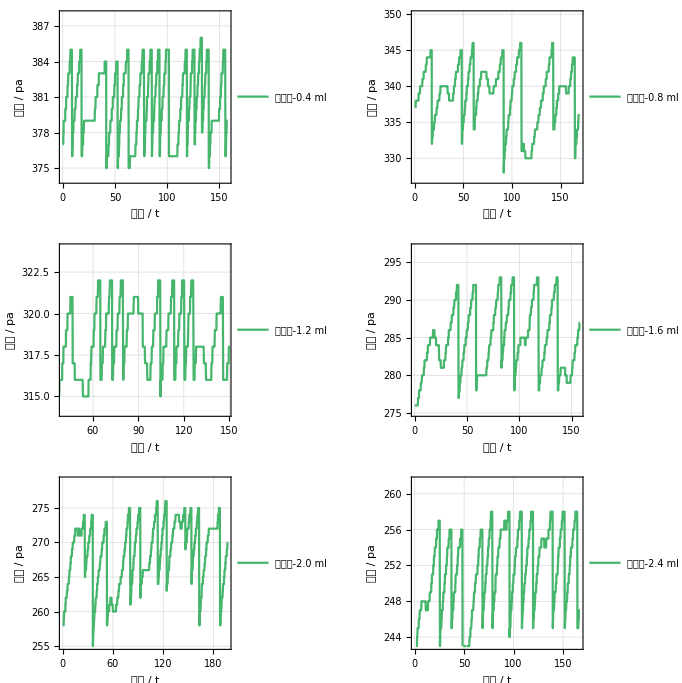

```mathematica
plotassenble = GraphicsGrid[Partition[Drop[images,1],2],ImageSize->Large]
```

```mathematica
Export["plot_all.jpg",plotassenble]
Export["plot_water.jpg",images[[1]]]
```

## 分析

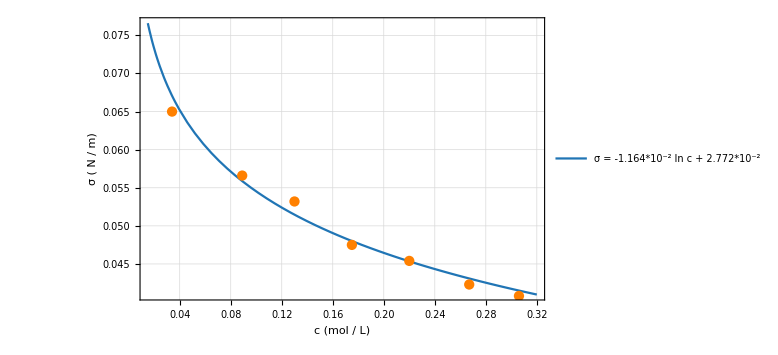

```mathematica
sigma={{0.034,65*10^-3},{0.089,56.6*10^-3},{0.13,53.2*10^-3},{0.175,47.5*10^-3},{0.22,45.4*10^-3},{0.267,42.3*10^-3},{0.306,40.8*10^-3}};
sig=ListPlot[sigma,PlotStyle->Orange];
moel=Plot[-1.164*10^-2 Log[c]+2.772*10^-2,{c,0.015,0.32},Frame -> True, LabelStyle
     -> Directive[Black], GridLines -> Automatic, PlotLegends -> Placed[LineLegend[
    {"σ = -1.164*10^-2 ln c + 2.772*10^-2"}, LegendFunction -> Frame], {0.75,0.9}],FrameLabel->{"c (mol / L)","σ ( N / m)"}, PlotStyle -> ColorData[
    99, "ColorList"],PlotStyle->Thickness[0.01],FrameStyle->Thickness[0.003]];
Show[moel,sig]
```

```mathematica
table = Table[{c,1.971*10^5 c-3.714+RandomReal[{-0.01,0.01}]},{c,{0.044,0.08,0.13,0.175,0.22,0.263,0.31}}];
```

{{0.044,8668.68},{0.08,15764.3},{0.13,25619.3},{0.175,34488.8},{0.22,43358.3},{0.263,51833.6},{0.31,61097.3}}

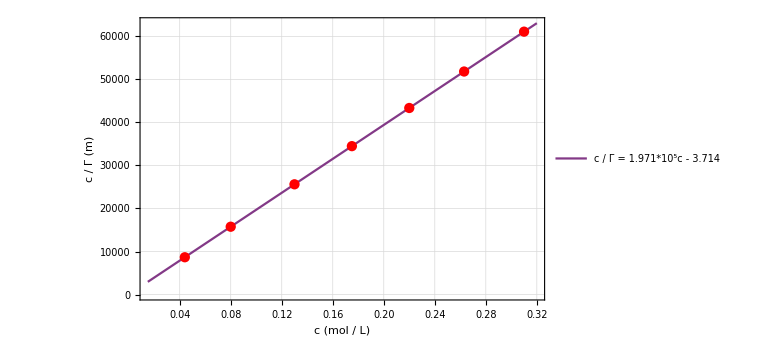

```mathematica
Show[Plot[1.971*10^5 c-3.714,{c,0.015,0.32},Frame -> True, LabelStyle
     -> Directive[Black], GridLines -> Automatic, PlotLegends -> Placed[LineLegend[
    {"c / Γ = 1.971*10^5c - 3.714"}, LegendFunction -> Frame], {0.225,0.9}],FrameLabel->{"c (mol / L)","c / Γ (m)"}, PlotStyle -> ColorData[
    99, "ColorList"][[9]],PlotStyle->Thickness[0.01],FrameStyle->Thickness[0.003],ImageSize->Large],ListPlot[table,PlotStyle->Red]]
```

```mathematica
data
```

{{{0.1,428},{0.2,428},{0.4,428},{0.6,428},{0.8,428},{1,428},{1.2,428},{1.3,428},{1.5,428},{1.6,428},{1.8,428},{2,428},{2.1,428},{2.2,428},979,{176,445},{176.2,445},{176.3,445},{176.5,431},{176.7,431},{176.9,431},{177.1,431},{177.3,432},{177.5,432},{177.7,432},{177.8,433},{178,433},{178.2,433},{178.3,433}},5,{1}}
 |  |  |  |

```mathematica
Mod[45251,8]
```

3

```mathematica
TableRefine[rawdata_]:=Module[
	{i,l=Length[rawdata],out,a,b,c,d,k},
	out = rawdata;
	k = Mod[l,4];
    
    a = Take[out,IntegerPart[l/4]+If[k==0,0,1]];
    b = Take[out,{IntegerPart[l/4]+If[k==0,0,1]+1,2*IntegerPart[l/4]+If[k==1,0,1]}];
    c = Take[out,{2*IntegerPart[l/4]+If[k==1,0,1],3*IntegerPart[l/4]+If[k==2,0,1]}];
    d = Take[out,{3*IntegerPart[l/4]+If[k==2,0,1]+1,l}];
    Join[a,b,c,d,2]
]

LatexTable[datalist_]:=Module[
	{table,textable,i,l = If[Mod[Length[datalist],4]==0,Length[datalist]/4,Length[datalist]/4+1]},
	table = TableRefine[datalist];
	For[i=1,i<=l,i++,
		If[i==1,
			textable = {StringReplace[ToString[table[[1]]],{","->"  & ","{"->"","}"->"  \\\\"}]},
			textable = Join[textable,{StringReplace[ToString[table[[i]]],{","->"  & ","{"->"","}"->"  \\\\"}]}]
		];
	];
	
	textable
]
```

```mathematica
out = Array[x,7];
For[i=1,i<=7,i++,
	out[[i]] = LatexTable[data[[i]]]
]

Length[out1]
Length[out2]
```

504

458

```mathematica
For[i=1,i<=7,i++,
	Export["/Users/royalty/Desktop/dump"<>ToString[i]<>".txt",out[[i]]]
	
]
```